# NV-Centre ESR Simulation

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### Usage-manual

Since Mathematica notebooks work in a cell-format, the simulation is split up into compartmentalized sections. The first section NV-Centre ESR Simulation contains the main code and functionality of the simulation. Before starting any simulation, you should first initialize it by executing this section (click on the rightmost collapsable bracket of the section, and then press Shift+Enter).

Consult the NV-Centre ESR Simulation → Functions subsection for the documentation on how to use each function.

The subsequent section is Simulations, consisting of individual instances of the simulation, each with different parameters. No spin-bath runs the simulation on an isolated NV-center. The Truncated Hamiltonian (m_s= 0, +1) (No spin-bath) runs the simulation on an isolated NV-center with a truncated Hamiltonian, only consider the m_s= 0, +1 states. The parameters of a simulation is set in the Initialisation subsection. You can tweak the simulation frequency-band, the frequency-resolution, the Hamiltonian, and everything else in there.

The Save simulation data subsection of a simulation saves the results into a folder called results in the notebook directory (if this directory doesn’t already exist, you need to create it). All simulation data is stored into separate folders, containing multiple files. To load the results of a previous simulation into the notebook, you can use the LoadSimulationData function.

To run a simulation, simply selection the whole section, and press Shift+Enter. Note that it’s not advised to run Evaluate Notebook, as this would evaluate all simulations.

To create a new simulation, simply copy one of the premade simulations and use it as a template.

### How the simulation works

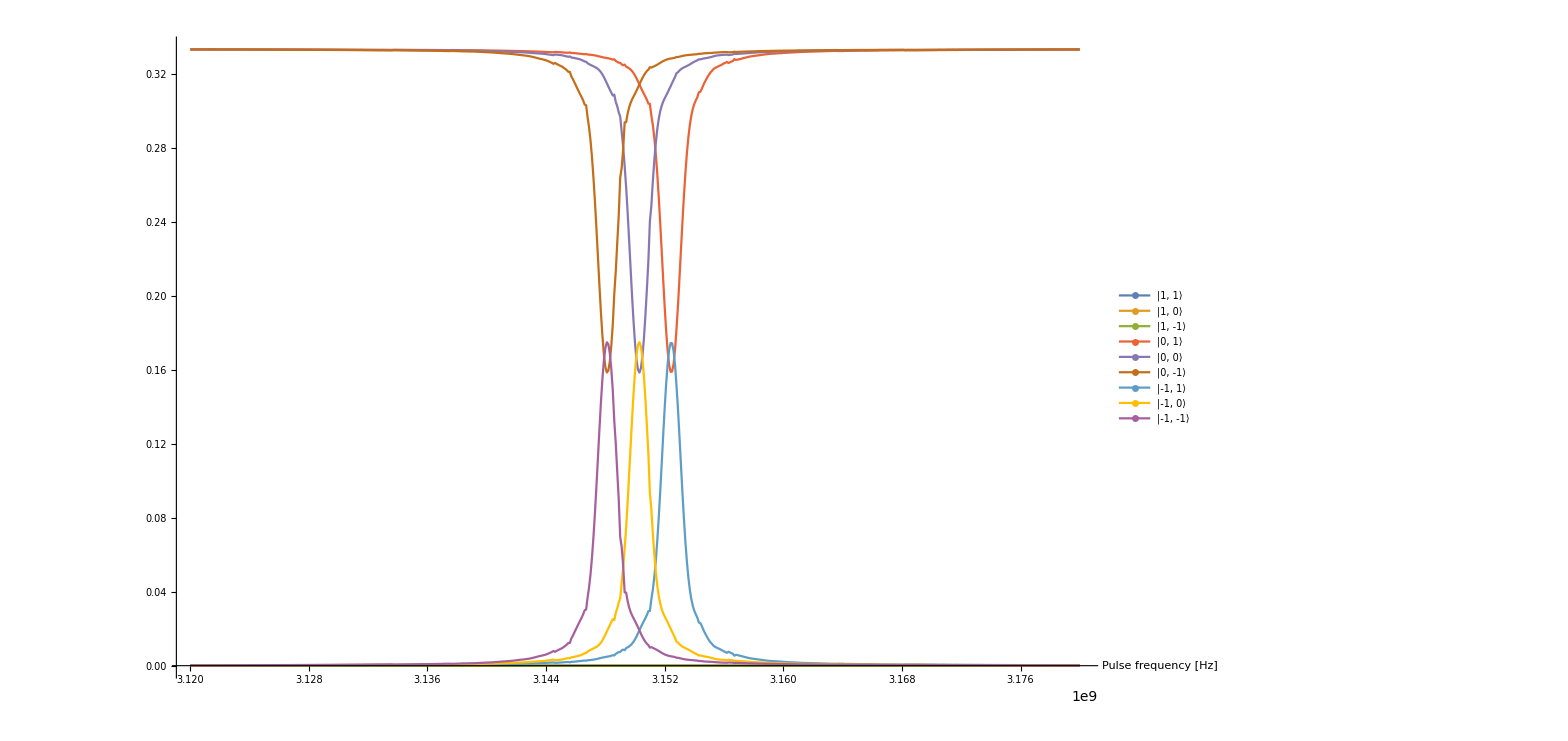
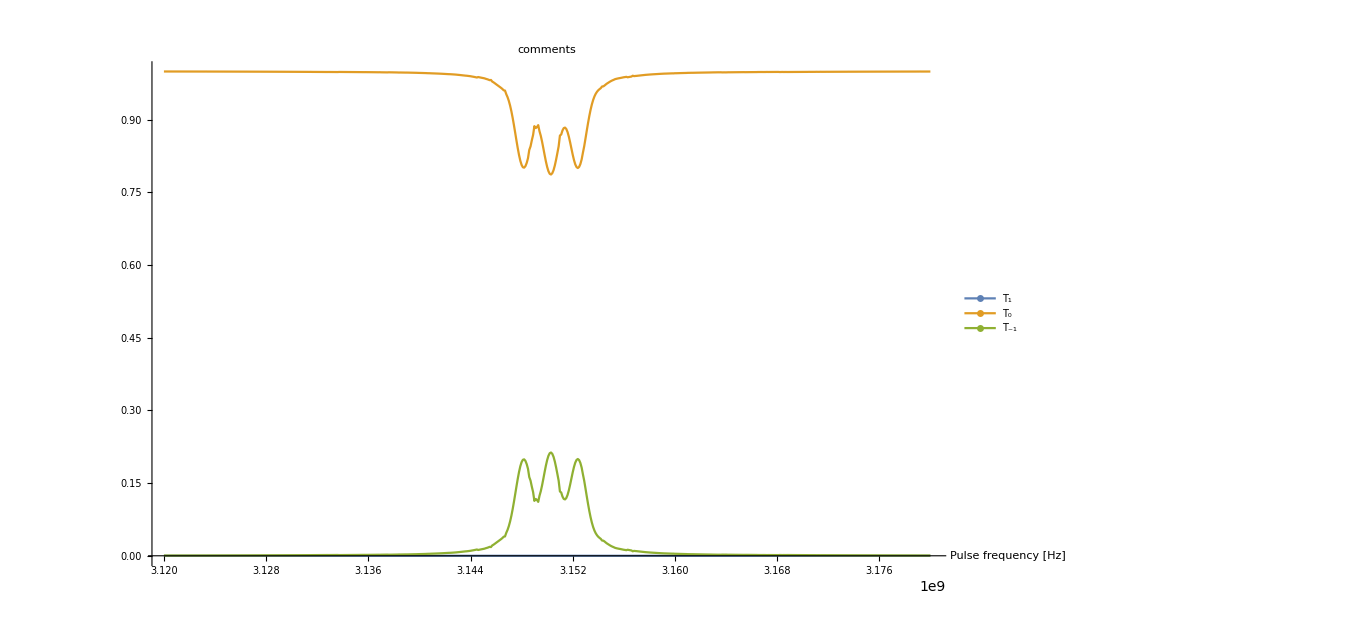
The time-evolution equation of a density matrix in the Schrödinger picture is

-Graphics-

which is the von Neumann equation. By adding a dephasing term, we get get a quantum master equation. The system under consideration is the ground-state of the NV-center (Nitrogen-15), which can be considered as two interacting spin-1 particles. The Hamiltonian for the system is the ground-state of the NV-center:

-Graphics-

The simulation supports any kind of Hamiltonian, and isn’t necessarily restricted to H_NV. For example, we could also consider a more complicated system consisting of the NV-center interacting with a set of other spins. We add a perturbing term to the Hamiltonian, an oscillating magnetic field (EM-wave) on an axis perpendicular to the principle axis of the ground-state

-Graphics-

where the phase ϕ is a simulation parameter, and the frequency f is 

The total Hamiltonian is then

-Graphics-.

The goal of the simulation is to produce a plot of the response of the system to a perturbation with frequency f. For a system starting from a electron triplet-0 state (T_0), we’d expect a dip in the probability of the system inhabiting the T_0 after the perturbation, for a for a frequency f corresponding to appropriate energies. The simulation sweeps through frequencies between a starting frequency freqStart and freqEnd (with a specified resolution freqStep). For each frequency f, the simulation evolves an initial state ρ(0) from a starting time tStart to an ending time tEnd. We then calculate the time-average for the system to inhabit each state |m_s, m_i⟩

-Graphics-

The following graph shows a result of one of these simulations.

-Graphics-

Where the vertical axis is the time-averaged probability, and the horizontal axis the frequency of the perturbation. Taking the partial trace of the system, only considering the electron-triplet, we can plot P(T_1),P(T_0) and P(T_-1):

-Graphics-

## Initialisation

## Standard spin operators

Define some useful spin-operators.

```mathematica
(* Spin operators *)
Sx = 1/Sqrt[2]{ {  0, 1, 0} , { 1, 0, 1}, {0, 1, 0 } };
Sy = {{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}};
Sz = { {1, 0, 0 }, {0, 0, 0}, {0, 0, -1}};
eye = IdentityMatrix[3];

(* Electron triplet operators *)

eSx = KroneckerProduct[Sx, eye];
eSy = KroneckerProduct[Sy, eye];
eSz = KroneckerProduct[Sz, eye];

(* Nuclear operators *)

Ix = KroneckerProduct[eye, Sx];
Iy = KroneckerProduct[eye, Sy];
Iz = KroneckerProduct[eye, Sz];

(* Total angular momentum *)

Jx = eSx + Ix;
Jy = eSy + Iy;
Jz = eSz + Iz;
```

## Functions

#### GetFirstSubsystem[density, subSystemSize]

For a density matrix ρ in the space V = A_1 ⊗ A_2 ⊗ ... ⊗ A_n, the function will return the reduced density matrix ρ_A_1.

Parameters:
- density [Matrix] - The density matrix is an n-by-n matrix, where n = dim(V).
- subSystemSize [Integer] - The dimension of A_1, dim(A_1).

```mathematica
GetFirstSubsystem[density_,subSystemSize_]:=Map[Tr,Partition[density,{Length[density]/subSystemSize,Length[density]/subSystemSize}],{2}];
```

#### FullHilbertSpaceOperator[operators, hilbertSubspaces]

Returns the matrix representation of an operator (Ô)_1⊗(Ô)_2⊗...⊗(Ô)_n.

Parameters:
- operators [List{ j [Integer] → op [Matrix], ...}] - A list of pairs. The second element of each pair is the matrix representation of the operator (Ô)_j, and the first element is the index j. Any unspecified operators for the subspaces will be replaced by an identity matrix of the appropriate size.
- hilbertSubspaces [List{Integer}] - A list of the dimensions of the subspaces j = 1, 2, ..., n.

Example:

Consider a system of two spin-1 particles, inhabiting Hilbert spaces V_1 and V_2 respectively, each of dimension 3. The total space is then V_1⊗ V_2. The following code will create the operator (Ŝ)_z⊗ (Ŝ)_z.

hilbertSubspaces = {3, 3};
Sz = SpinMatrixZ[1];
SzSz = FullHilbertSpaceOperator[ {1 → Sz, 2 → Sz }, hilbertSubspaces];

The variable operators should contain a list of pairs, where the second element is the operator acting on subsystem i, and where the first element is i. hilbertSubspaces is a list of the dimensions of the subspaces. Any unspecified operators for the subspaces will be replaced by an identity matrix of the appropriate size.

```mathematica
FullHilbertSpaceOperator[elem_ /; IntegerQ[elem[[1]]], hilbertSubspaces_] := FullHilbertSpaceOperator[{elem}, hilbertSubspaces];

FullHilbertSpaceOperator[ops_:{ elem_ /; IntegerQ[elem[[1]]] ..} , hilbertSubspaces_] := Module[
{operator = {1}, next},
Do[

next = Select[ ops, #[[1]] == i &];
next = If[next == {}, IdentityMatrix[hilbertSubspaces[[i]]], next[[1]][[2]]];
operator = KroneckerProduct[operator, next];
,{i, 1, Length[hilbertSubspaces]}];

operator
];
```

#### SpinMatrixX[spin]

Returns the spin matrix (Ŝ)_X, for a given spin.

Parameters:
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrixX[spin_] :=Table[
(i,j+1  + i+1,j)1/2 Sqrt[spin(spin+1) - i*j]
,{i, spin, -spin,-1},{j,spin, -spin, -1}]
```

#### SpinMatrixY[spin]

Returns the spin matrix (Ŝ)_Y, for a given spin.

Parameters:
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrixY[spin_] :=Table[
(i,j+1  - i+1,j)1/(2 I)Sqrt[spin(spin+1) - i*j]
,{i, spin, -spin, -1},{j, spin, -spin, -1}]
```

#### SpinMatrixZ[spin]

Returns the spin matrix (Ŝ)_Z, for a given spin.

Parameters:
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrixZ[spin_] :=Table[
i,j  j
,{i, spin, -spin, -1},{j, spin, -spin, -1}]
```

#### SpinMatrix[j, spin]

Returns the spin matrix (Ŝ)_j, for a given spin.

Parameters:
- j [Integer] - The axis of the projection.
- spin [Rational] - The spin of the particle. The dimension of the matrix will be 2*spin + 1.

```mathematica
SpinMatrix[j_/; Mod[j-1, 3] == 0, spin_] := SpinMatrixX[spin];
SpinMatrix[j_/; Mod[j-1, 3] == 1, spin_] := SpinMatrixY[spin];
SpinMatrix[j_/; Mod[j-1, 3] == 2, spin_] := SpinMatrixZ[spin];
```

#### SpinSpinHamiltonian[spins, couplings]

Returns a Hamiltonian of the form ∑_ij (k_(ij,x) (Ŝ)_(i,x)(Ŝ)_(j,x) + k_(ij,y) (Ŝ)_(i,y)(Ŝ)_(j,y) + k_(ij,z) (Ŝ)_(i,z)(Ŝ)_(j,z)), representing n interacting spins.

Parameters:
spins [List{Rational}] - An ordered list of spins {spin1, spin2, ...} in the system.
couplings [List{ { i [Integer] → j [Integer], coupling [Float or 3-vector] }, ... }] - List of elements of the form {subsystemIndexOfSpin1 → subsystemIndexOfSpin2, coupling}. coupling could either be a single Floating point constant, for an isotropic spin-spin coupling, or a 3-vector {A_x, A_y, A_z} for an anisotropic coupling.

Example:
We have three interacting spin-1/2 particles labelled i = 1, 2, 3. The interactions 1 ↔ 2 and 1 ↔ 3 are isotropic, but 2 ↔ 3 is anisotropic. Particle 1 has a zero-field-splitting D. The following code creates the Hamiltonian of the system.

ℋspinSpin =  SpinSpinHamiltonian[
   spins,
   {{1 → 1, {0, 0, D}},
    {1 → 2, k12},
    {1 → 3, k13},
    {2 → 3, {k23x, k23y, k23z}}}
] ;

```mathematica
SpinSpinHamiltonian[spins_, couplings_ : { { _ -> _,  _} ..}] := Module[
{H, spin1, spin2, sx, sy,sz, i, j, coeffs},

H = ConstantArray[0, {Times @@ (2spins + 1),Times @@ (2spins + 1)}];

Do[
i = c[[1]][[1]] ;
j = c[[1]][[2]] ;
coeffs = {};

Which[
NumberQ[c[[2]]],
coeffs = {c[[2]], c[[2]], c[[2]]},
Length[c[[2]]] == 3,
coeffs = c[[2]]
];

H = H + Sum[
coeffs[[k]]*FullHilbertSpaceOperator[ 
i->  SpinMatrix[k, spins[[i]]],
2*spins+1
] .FullHilbertSpaceOperator[ 
j ->  SpinMatrix[k, spins[[j]]],
2*spins+1
]
,{k, 1, 3}];

,{c, couplings}];
H
];
```

#### ZeemanHamiltonian[spins, ωs]

Returns a Zeeman Hamiltonian for the specified spins, of the form ∑_i ω_i(Ŝ)_(i,z).

Parameters:
- spins [List{Rational}] - An ordered list of spins {spin1, spin2, ...} for each particle.
- ωs [List{Float}] - An ordered list of Zeeman constants corresponding to each spin.

```mathematica
ZeemanHamiltonian[spins_, ωs_] :=Sum[
ωs[[i]]*FullHilbertSpaceOperator[i ->  SpinMatrixZ[spins[[i]]], 2spins+1]
,{i, 1, Length[spins]}]
```

#### NVCenterEnergySpectrum[ℋ, spins]

Returns the energy spectrum of the ground-state of the NV-center.

Parameters:
ℋ [9x9 Matrix] - A 9x9 in a |m_s, m_i⟩ basis, representing the ground-state of the NV-center.

Returns:
List : {data, table}

data is a list structured as follows:

data = {
	energies,
	vecDecomps,
	states,
	angMoms
};

table is a stylized representation of the energy spectrum, for example:

("E" | "|ψ_E⟩" | "⟨J_z⟩"
"---" | "---" | "---"
3.15026×10^9 | {-0.00066556 "|0,-1⟩",1. "|-1,0⟩"} | -1.
3.1475×10^9 | {2.49943×10^-6 "|1,-1⟩",-0.000667198 "|0,0⟩",1. "|-1,1⟩"} | 0.
3.14312×10^9 | {1. "|-1,-1⟩"} | -2.
2.58975×10^9 | {1. "|1,0⟩",-0.000809353 "|0,1⟩"} | 1.
2.58692×10^9 | {1. "|1,-1⟩",-0.000811772 "|0,0⟩",-3.04104×10^-6 "|-1,1⟩"} | 0.
2.58266×10^9 | {1. "|1,1⟩"} | 2.
-3105.84 | {0.000811774 "|1,-1⟩",0.999999 "|0,0⟩",0.000667196 "|-1,1⟩"} | 0.
-4.92093×10^6 | {0.000809353 "|1,0⟩",1. "|0,1⟩"} | 1.
-4.98216×10^6 | {1. "|0,-1⟩",0.00066556 "|-1,0⟩"} | -1.)

```mathematica
NVCenterEnergySpectrum[ℋ_] := Module[
{basis, mult = 2spins + 1, eig, energies, states,vecDecomps , vecsIndices, vecs, strs,
coeff, label,Jz, angMoms, table, data, spins = {1, 1} },
basis[indices_]:= Apply[KroneckerProduct, Table[
RotateRight[Flatten[IdentityMatrix[{1,mult[[i]]}]], indices[[i]]  - 1]
,{i, 1, Length[spins]}]] // Flatten;

eig = Eigensystem[ℋ];
energies = eig[[1]];
states = eig[[2]];

vecDecomps = {};
Do[
vecsIndices = Tuples[Map[Range, mult]];
vecs = Map[ basis, vecsIndices];
strs = {};
Do[
coeff = Conjugate[vecs[[i]]] . states[[k]];
label = Style["|"<>StringRiffle[Table[ (spins[[j]]-vecsIndices[[i]][[j]] + 1)//Rationalize, {j, 1, Length[spins]}],","]<>"⟩", Bold];

If[ coeff ≠ 0, AppendTo[strs,coeff * label]];
,{i, 1, Length[vecsIndices]}];

AppendTo[vecDecomps, strs];
,{k, 1, Length[states]}];

Jz = FullHilbertSpaceOperator[{1 -> SpinMatrixZ[spins[[1]] ]}  , mult] +
FullHilbertSpaceOperator[{2 -> SpinMatrixZ[spins[[2]] ]}  ,mult];
angMoms = Map[ # . Jz . # &, states];

data = {
energies,
vecDecomps,
states,
angMoms
};

data = Sort[Transpose[data], #1[[1]] > #2[[1]] &] // Transpose; 

table = {
Prepend[Prepend[data[[1]], "---"], Style["E", Bold]],
Prepend[ Prepend[data[[2]], "---"], Style["|ψ_E⟩", Bold]],
Prepend[Prepend[data[[4]], "---"],  Style["⟨J_z⟩", Bold]]
} // Transpose //MatrixForm;
{data, table}
];
```

#### NVCenterEnergySpectrum2[ℋ, spins]

Returns the energies of |m_s, m_i⟩ states for the given Hamiltonian. The main difference between this function and NVCenterEnergySpectrum is that the former returns the actual energy-eigenvalues of the Hamiltonian. Since the |m_s, m_i⟩ states aren’t necessarily the energy-eigenstates of the Hamiltonian, NVCenterEnergySpectrum and NVCenterEnergySpectrum2 yield different results.

Parameters:
ℋ [9x9 Matrix] - A 9x9 in a |m_s, m_i⟩ basis, representing the ground-state of the NV-center.

Returns:

List : {data, table}

data is a list structured as follows:

data = {
	energies,
	vecDecomps,
	states,
	angMoms
};

table is a stylized representation of the energy spectrum, for example:

("E" | "|ψ_E⟩" | "⟨J_z⟩"
"---" | "---" | "---"
3.15026×10^9 | "|-1,0⟩" | -1
3.1475×10^9 | "|-1,1⟩" | 0
3.14312×10^9 | "|-1,-1⟩" | -2
2.58974×10^9 | "|1,0⟩" | 1
2.58692×10^9 | "|1,-1⟩" | 0
2.58266×10^9 | "|1,1⟩" | 2
0. | "|0,0⟩" | 0
-4.91923×10^6 | "|0,1⟩" | 1
-4.98077×10^6 | "|0,-1⟩" | -1)

```mathematica
NVCenterEnergySpectrum2[ℋ_] := Module[
{basis, mult = 2spins + 1, eig, energies, states,vecDecomps , vecsIndices, vecs, strs,
coeff, label,Jz, angMoms, table, data  , spins={1,1}},
basis[indices_]:= Apply[KroneckerProduct, Table[
RotateRight[Flatten[IdentityMatrix[{1,mult[[i]]}]], indices[[i]]  - 1]
,{i, 1, Length[spins]}]] // Flatten;

states = IdentityMatrix[Length[ℋ]];
energies = Table[Conjugate[s] .ℋ . s,{s, states}];

vecDecomps = {};
Do[
vecsIndices = Tuples[Map[Range, mult]];
vecs = Map[ basis, vecsIndices];
strs = {};
Do[
coeff = Conjugate[vecs[[i]]] . states[[k]];
label = Style["|"<>StringRiffle[Table[ (spins[[j]]-vecsIndices[[i]][[j]] + 1)//Rationalize, {j, 1, Length[spins]}],","]<>"⟩", Bold];

If[ coeff ≠ 0, AppendTo[strs,coeff * label]];
,{i, 1, Length[vecsIndices]}];

AppendTo[vecDecomps, strs[[1]]];
,{k, 1, Length[states]}];

Jz = FullHilbertSpaceOperator[{1 -> SpinMatrixZ[spins[[1]] ]}  , mult] +
FullHilbertSpaceOperator[{2 -> SpinMatrixZ[spins[[2]] ]}  ,mult];
angMoms = Map[ # . Jz . # &, states];

data = {
energies,
vecDecomps,
states,
angMoms
};

data = Sort[Transpose[data], #1[[1]] > #2[[1]] &] // Transpose; 

table = {
Prepend[Prepend[data[[1]], "---"], Style["E", Bold]],
Prepend[ Prepend[data[[2]], "---"], Style["|ψ_E⟩", Bold]],
Prepend[Prepend[data[[4]], "---"],  Style["⟨J_z⟩", Bold]]
} // Transpose //MatrixForm;
{data, table}
];
```

#### RunSimulation[freqStart, freqEnd, freqStep, tStart, tEnd, ℋ, basisStates, density0, dephasing]

Runs the ESR simulation on the given Hamiltonian. The function doesn’t return any values, but rather sets the variable simData with the results of the simulation. After running the function, the results can be accessed in the following DownValues:

simData[i,j] (*with i,j=1,0,-1,for the states|1,1⟩|1,0⟩|1,-1⟩|0,1⟩|0,0⟩|0,-1⟩|-1,1⟩|-1,0⟩|-1,-1⟩) *)
simData[“allstates”] (* Contains the data for all the states in canonical order *)
simData[“totalSimulationTime”] (* The total runtime of the simulation *)

Parameters:
freqStart [Float] - Starting frequency.
freqEnd [Float] - End frequency
freqStep [Float] - The resolution of the simulation.
tStart [Float] - The starting time of the perturbation.
tEnd [Float] - The end time of the perturbation.
ℋ [Matrix] - The time-dependent Hamiltonian to run the simulation with. The Hamiltonian ℋ[f, t] must be a function of time t and frequency f.
density0 [Matrix] - The initial state of the system.
dephasing [Matrix] - The dephasing coefficients.

```mathematica
RunSimulation[freqStart_, freqEnd_, freqStep_, tStart_, tEnd_, ℋ_, basisStates_, density0_, dephasing_] := Module[
{calculations,systemSize, density, eqnTotal, eqns, diffeqs, funcs, initialStateEqs, params, subsystem,
data, tic, count, sol, pulseFreq, pFunc, p, prw, toc, ttot, system1, dephasingmatrix},

calculations = Table[f, {f, freqStart, freqEnd, freqStep}] // Length;

(* Setup Density matrix *)

systemSize = Length[density0];
density = Table[ ρ[i, j][t],{i, 1, systemSize}, {j, 1, systemSize}] ;
Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, systemSize}, {j, i+1, systemSize}];

(* Define master equation *)

dephasingmatrix = Table[density[[i, j]] dephasing[[i, j]], {i, 1, Length[density]},  {j, 1, Length[density]}];

eqnTotal = ⅈ  D[ density, t] - (ℋ[f, t].density - density.ℋ[f, t]) - dephasingmatrix// Simplify;

eqns = Table[ eqnTotal[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
initialStateEqs =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, initialStateEqs } // Flatten;

(* Perform simulation *)

tic=AbsoluteTime[];
count = 1;

data =Table[ {}, {i, 1, Length[basisStates]}]; (* Store spinVec probability data for each frequency *)
Do[
simData[i] = {};
,{i, 1, Length[basisStates]}];

plot =Dynamic[ListPlot[data, Joined->True, PlotMarkers->Automatic,PlotLegends -> Automatic], TrackedSymbols:>{data}];
Print[plot];

Do[
sol = NDSolve[ params /. f -> freq, funcs, {t, tStart, tEnd}, 
PrecisionGoal->7,AccuracyGoal->7, MaxSteps->Infinity];

Do[
system1 = GetFirstSubsystem[density, Length[basisStates[[1]]]  ]; (*  Length[basisStates[[1]]] is the dimension of the subsystem. *)
pFunc = Conjugate[basisStates[[i]]] .system1. basisStates[[i]];
p = 1/(tEnd - tStart)NIntegrate[pFunc /. sol, {t, tStart, tEnd}] //Abs;
AppendTo[data[[i]], {freq, p[[1]]}];
AppendTo[simData[i], {freq, p[[1]]}];
, {i, 1, Length[basisStates]}];

NotebookDelete[prw];
prw = PrintTemporary["Calculation ", count, " out of ", calculations];
count = count + 1;

, {freq, freqStart, freqEnd, freqStep}];

toc=AbsoluteTime[];
ttot = N[(toc-tic)/60];
Print["Total time taken (min) = ",ttot];
simData["totalSimulationTime"] = ttot;
simData["allstates"] = data;
];
```

#### SolveSystem[tStart, tEnd, ℋ, freq, density0]

Returns a solution to the quantum master equation for a given Hamiltonian.

Parameters:
freq [Float] - The frequency of the perturbation.
tStart [Float] - The starting time of the perturbation.
tEnd [Float] - The end time of the perturbation.
ℋ [Matrix] - The time-dependent Hamiltonian to run the simulation with. The Hamiltonian ℋ[f, t] must be a function of time t and frequency f.
density0 [Matrix] - The initial state of the system.
dephasing [Matrix] - The dephasing coefficients.

Returns:
List : {density, sol, stateFuncs}

density is a representation of the density matrix. For example:

(ρ[1,1][t] | ρ[1,2][t] | ρ[1,3][t] | ρ[1,4][t]
Conjugate[ρ[1,2][t]] | ρ[2,2][t] | ρ[2,3][t] | ρ[2,4][t]
Conjugate[ρ[1,3][t]] | Conjugate[ρ[2,3][t]] | ρ[3,3][t] | ρ[3,4][t]
Conjugate[ρ[1,4][t]] | Conjugate[ρ[2,4][t]] | Conjugate[ρ[3,4][t]] | ρ[4,4][t])

sol is the solution of the quantum master equation, under the given simulation parameters. As usual for Mathematica, the solution is represented as a list of rules, and should be applied on density to extract the functions.

stateFuncs are the probability functions P(m_s, m_i, t).

```mathematica
SolveSystem[tStart_, tEnd_, ℋ_,freq_, density0_ , basisStates_ , dephasing_] := Module[
{systemSize, density, eqnTotal, eqns, diffeqs, funcs, initialStateEqs, params, sol, stateFuncs, dephasingmatrix, subSystem},
(* Setup Density matrix *)
systemSize = Length[density0];
density = Table[ ρ[i, j][t],{i, 1, systemSize}, {j, 1, systemSize}] ;

dephasingmatrix = Table[density[[i, j]] dephasing[[i, j]], {i, 1, Length[density]},  {j, 1, Length[density]}];

Do[
density[[j, i]] = Conjugate[density[[i,j]]];
, {i, 1, systemSize}, {j, i+1, systemSize}];

(* Define master equation *)

eqnTotal = ⅈ  D[ density, t] - (ℋ[f, t].density - density.ℋ[f, t]) - dephasingmatrix // Simplify;

eqns = Table[ eqnTotal[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
diffeqs = Table[ eqns[[i]] == 0, {i, 1, Length[eqns]}];
funcs =Table[ density[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}] // Flatten;
initialStateEqs =  Table[ ρ[i, j][0] == density0[[i, j]],  {i, 1, systemSize}, {j, i, systemSize}]  // Flatten;
params = { diffeqs, initialStateEqs } // Flatten;

sol = NDSolve[ params /. f -> freq, funcs, {t, tStart, tEnd}, 
PrecisionGoal->7,AccuracyGoal->7, MaxSteps->Infinity];

subSystem = GetFirstSubsystem[density, Length[basisStates[[1]] ]];
stateFuncs = Table[
Conjugate[state] . subSystem . state  /. sol // Flatten,
{state, basisStates}];

{density, sol, stateFuncs}
];
```

#### LoadSimulationData[dir]

When running the simulation, data is exported into separate folders. This function will load simulation data from a specific run, given the folder directory path. The path could either be the full path, or a relative path from the current notebook directory.

Parameters:
dir [String] - The path to the directory of the simulation data.

Example:
The function will return a variable that contains the data. The data is stored in the following DownValues:

simData=LoadSimulationData[dir]
simData[i,j] (*with i,j=1,0,-1,for the states|1,1⟩|1,0⟩|1,-1⟩|0,1⟩|0,0⟩|0,-1⟩|-1,1⟩|-1,0⟩|-1,-1⟩) *)
simData[“allstates”] (* Contains the data for all the states in canonical order *)

```mathematica
LoadSimulationData[dir_] := Module[
{simData, ms, mi, stateStr, pre},

simData["allstates"] = {};
pre = FileNameSplit[dir]//Last;

Do[
ms = 1- ( (i- 1)/3 // Floor);
mi = 1- Mod[i-1, 3];
stateStr = "state(" <> ToString[ms] <> "," <> ToString[mi] <>")";
simData[ms, mi] = Import[FileNameJoin[{ dir, pre<>"_data_"<> stateStr <> ".csv" }]];
AppendTo[simData["allstates"], simData[ms, mi]];
,{i, 1, 9}];

simData["T(1)"] =  Import[ FileNameJoin[{dir, pre <> "_data_T(1).csv"}]];
simData["T(0)"] =  Import[ FileNameJoin[{dir, pre <> "_data_T(0).csv"}]];
simData["T(-1)"] =  Import[ FileNameJoin[{dir, pre <> "_data_T(-1).csv"}]];

simData
]
```

# Simulations

## No spin-bath

### Initialisation

#### NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

#### Simulation parameters

```mathematica
pulseAmplitude = 1*10^6; (* [Hz] *)
pulseAmplitudeE = pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.575*^9; (* [Hz] *)
pulseFreqEnd =3.25*^9; (* [Hz] *) 
pulseFreqStep = 0.1*10^6; (* [Hz] *) 
calculations =Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 5*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 6751

#### Setup Hamiltonian

```mathematica
spins = {1, 1};
hilbertSubspaceDimensions = 2*spins + 1;
totalHilbertSpaceDimension = Apply[Times, hilbertSubspaceDimensions];

ℋHF =  SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋzfs =  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋzfs + ℋzee;

ℋCop =  (pulseAmplitudeE* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1] }, hilbertSubspaceDimensions ]  + pulseAmplitudeN * FullHilbertSpaceOperator[ { 2-> SpinMatrixX[1] }, hilbertSubspaceDimensions ] );

ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];

dephasing = ConstantArray[0, {totalHilbertSpaceDimension, totalHilbertSpaceDimension}];
Do[ dephasing[[i,i]] = 0, {i, 1, Length[dephasing]}]; (* Set the off-diagonal coefficients to 0 *)
```

#### Energy spectrum of the unperturbed Hamiltonian

In terms of the eigenstates of the Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV]; 
hamiltonianSpectrum[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | {-0.00066556 |0,-1⟩,1. |-1,0⟩} | -1.
3.1475×10^9 | {2.49943×10^-6 |1,-1⟩,-0.000667198 |0,0⟩,1. |-1,1⟩} | 0.
3.14312×10^9 | {1. |-1,-1⟩} | -2.
2.58975×10^9 | {1. |1,0⟩,-0.000809353 |0,1⟩} | 1.
2.58692×10^9 | {1. |1,-1⟩,-0.000811772 |0,0⟩,-3.04104×10^-6 |-1,1⟩} | 0.
2.58266×10^9 | {1. |1,1⟩} | 2.
-3105.84 | {0.000811774 |1,-1⟩,0.999999 |0,0⟩,0.000667196 |-1,1⟩} | 0.
-4.92093×10^6 | {0.000809353 |1,0⟩,1. |0,1⟩} | 1.
-4.98216×10^6 | {1. |0,-1⟩,0.00066556 |-1,0⟩} | -1.)

In terms of eigenstates of the spin triplet and nuclear spin

```mathematica
hamiltonianSpectrumPure = NVCenterEnergySpectrum2[ℋ[0,0]];
hamiltonianSpectrumPure[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | |-1,0⟩ | -1
3.1475×10^9 | |-1,1⟩ | 0
3.14312×10^9 | |-1,-1⟩ | -2
2.58974×10^9 | |1,0⟩ | 1
2.58692×10^9 | |1,-1⟩ | 0
2.58266×10^9 | |1,1⟩ | 2
0. | |0,0⟩ | 0
-4.91923×10^6 | |0,1⟩ | 1
-4.98077×10^6 | |0,-1⟩ | -1)

#### Initial state

```mathematica
density0 = 1/3(Outer[Times,  IdentityMatrix[9][[4]],  IdentityMatrix[9][[4]]] + Outer[Times,  IdentityMatrix[9][[5]],  IdentityMatrix[9][[5]]] +Outer[Times,  IdentityMatrix[9][[6]],  IdentityMatrix[9][[6]]]);
```

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Rabi Oscillations

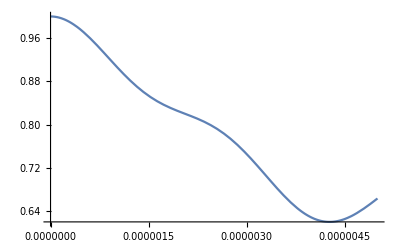

```mathematica
res = SolveSystem[ tStart, tEnd, ℋ,2.5897440607094812*^9, density0, IdentityMatrix[9], dephasing];
Plot[res[[3]][[4]] + res[[3]][[5]] + res[[3]][[6]], {t, tStart, tEnd}, PlotLegends->Automatic]
```

### Run simulation

```mathematica
NVbasisStates = IdentityMatrix[9];
RunSimulation[pulseFreqStart,pulseFreqEnd, pulseFreqStep, tStart, tEnd, ℋ,NVbasisStates,density0, dephasing]
totalSimulationTime = simData["totalSimulationTime"];

freqs = Table[ simData["allstates"][[1]][[i]][[1]],{i, 1, Length[simData["allstates"][[1]]]}];
simData["T(1)"]= Table[ {freqs[[i]],  simData["allstates"][[1]][[i]][[2]] + simData["allstates"][[2]][[i]][[2]] + simData["allstates"][[3]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(0)"]= Table[ {freqs[[i]],  simData["allstates"][[4]][[i]][[2]] + simData["allstates"][[5]][[i]][[2]] + simData["allstates"][[6]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(-1)"]= Table[ {freqs[[i]],  simData["allstates"][[7]][[i]][[2]] + simData["allstates"][[8]][[i]][[2]] + simData["allstates"][[9]][[i]][[2]]},  {i, 1, Length[freqs]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.82855095426441×10^-6}. NIntegrate obtained 3.77009×10^-9+0. ⅈ and 2.26226×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.00555×10^-7}. NIntegrate obtained 2.77294×10^-9+1.22698×10^-26 ⅈ and 1.81828×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.64555×10^-7}. NIntegrate obtained 2.1231×10^-9+0. ⅈ and 2.35676×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Total time taken (min) = 536.449

### Results

#### Full simulation results

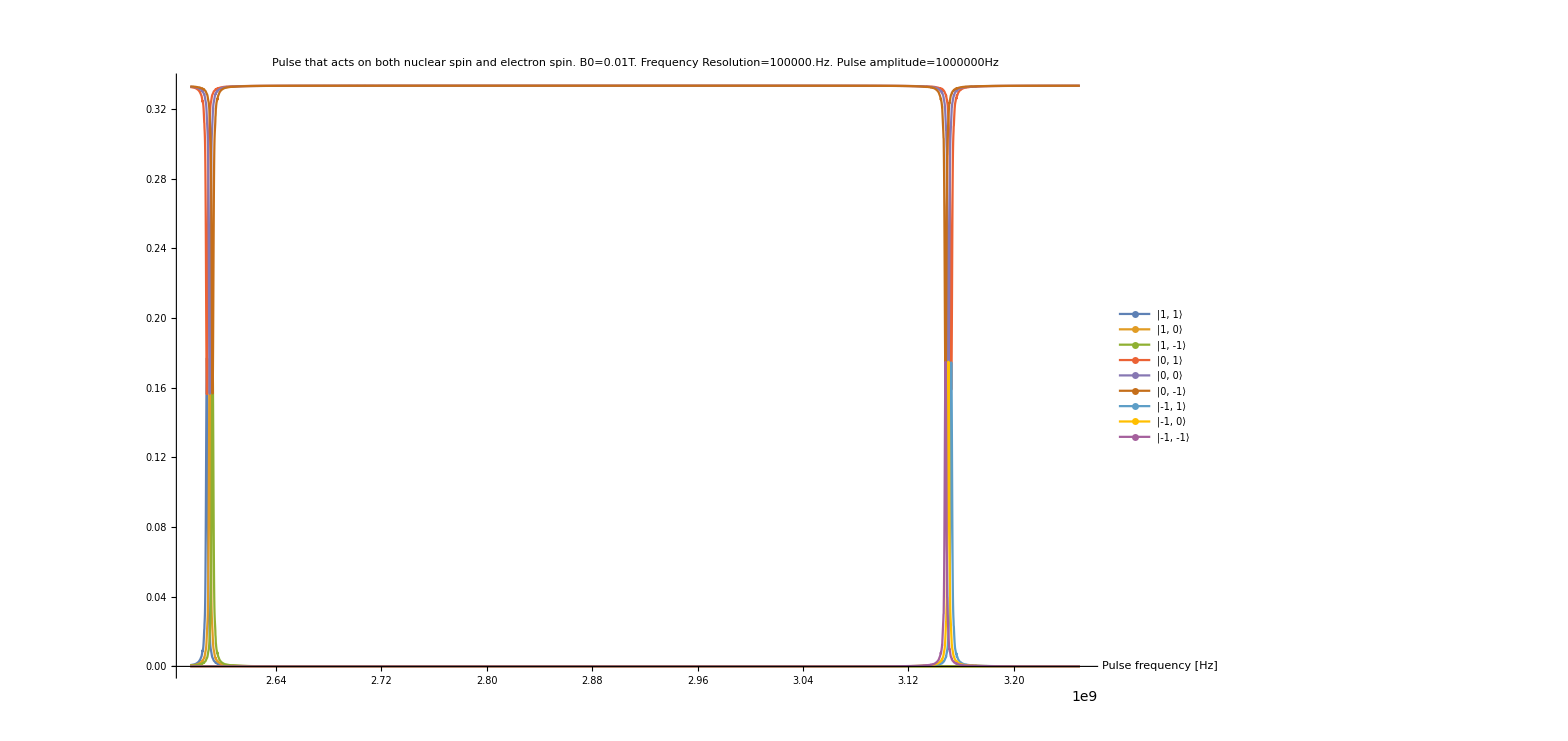

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
fullplot = ListPlot[simData["allstates"], PlotLegends ->LineLegend[fullPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full},Joined-> True,PlotMarkers->None, ImageSize -> 1200 ]
```

#### ESR Plot

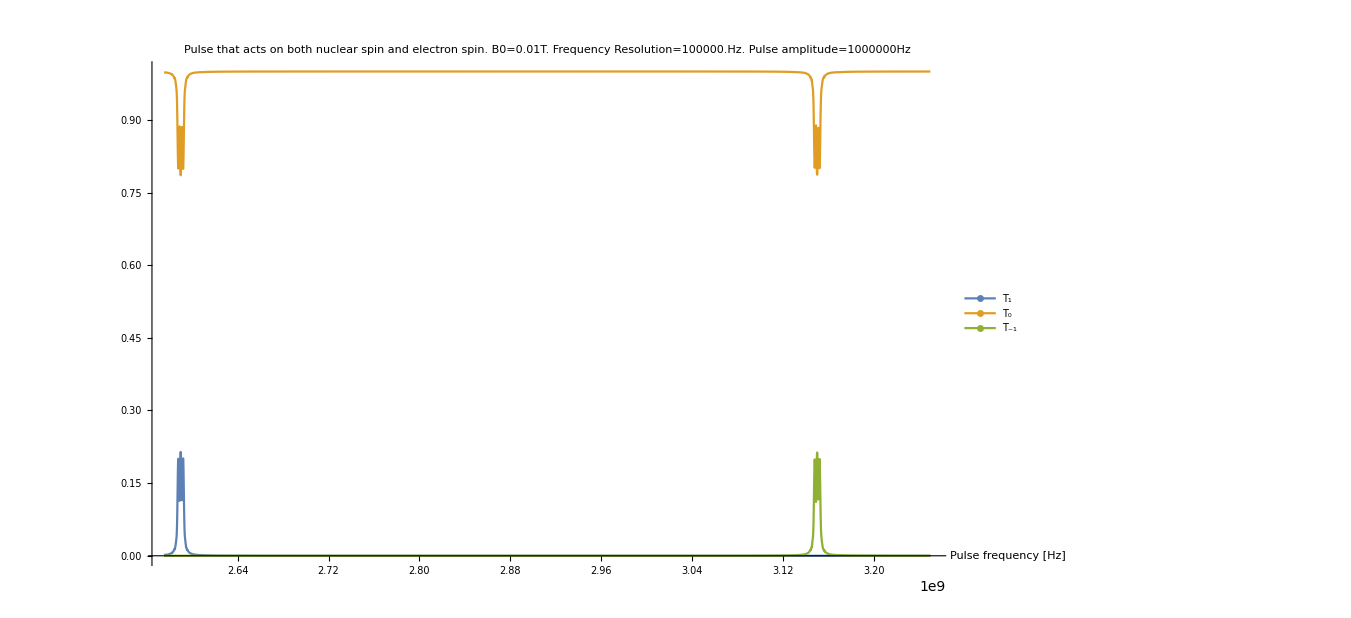

```mathematica
esrPlotlegend = {"T_1", "T_0", "T_-1"};
esrplot = ListPlot[{simData["T(1)"], simData["T(0)"], simData["T(-1)"]}, PlotLegends ->LineLegend[esrPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full}, ImageSize -> 1000 , Joined->True]
```

### Save simulation data

```mathematica
CreateDirectory["./" <> resultsFolder <> fileNamePrefix];
fpre =  "./" <> resultsFolder <> fileNamePrefix <> "/" <> fileNamePrefix;

Export[fpre<> "_data_T(1).csv",simData["T(1)"] ];
Export[fpre<> "_data_T(0).csv",simData["T(0)"]  ];
Export[fpre<> "_data_T(-1).csv",simData["T(-1)"]  ];

(* Save the ESR data *)
Do[
stateStr = "state(" <>ToString[1- ( (i- 1)/3 // Floor)] <> "," <> ToString[1- Mod[i-1, 3]] <>")";
Export[fpre<>"_data_"<> stateStr <> ".csv",simData[i] ];
,{i, 1, 9}]

Export[fpre<> "_spectrum.csv", hamiltonianSpectrum];
Export[fpre<> "_ESRplot.pdf", esrplot];
Export[fpre<> "_fullplot.pdf", fullplot];
Save[ fpre <> "_params.wl", {  comments, totalSimulationTime, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,dephasing,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs}];
```

## No spin-bath 2

### Initialisation

#### NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

#### Simulation parameters

```mathematica
pulseAmplitude = 1*10^6; (* [Hz] *)
pulseAmplitudeE = pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 3.10*^9; (* [Hz] *)
pulseFreqEnd =3.2*^9; (* [Hz] *) 
pulseFreqStep = 0.1*10^6; (* [Hz] *) 
calculations =Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 5*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 1001

#### Setup Hamiltonian

```mathematica
spins = {1, 1};
hilbertSubspaceDimensions = 2*spins + 1;
totalHilbertSpaceDimension = Apply[Times, hilbertSubspaceDimensions];

ℋHF =  SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋzfs =  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋzfs + ℋzee;

ℋCop =  (pulseAmplitudeE* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1] }, hilbertSubspaceDimensions ]  + pulseAmplitudeN * FullHilbertSpaceOperator[ { 2-> SpinMatrixX[1] }, hilbertSubspaceDimensions ] );

ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];

dephasing = ConstantArray[0, {totalHilbertSpaceDimension, totalHilbertSpaceDimension}];
Do[ dephasing[[i,i]] = 0, {i, 1, Length[dephasing]}]; (* Set the off-diagonal coefficients to 0 *)
```

#### Energy spectrum of the unperturbed Hamiltonian

In terms of the eigenstates of the Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV]; 
hamiltonianSpectrum[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | {-0.00066556 |0,-1⟩,1. |-1,0⟩} | -1.
3.1475×10^9 | {2.49943×10^-6 |1,-1⟩,-0.000667198 |0,0⟩,1. |-1,1⟩} | 0.
3.14312×10^9 | {1. |-1,-1⟩} | -2.
2.58975×10^9 | {1. |1,0⟩,-0.000809353 |0,1⟩} | 1.
2.58692×10^9 | {1. |1,-1⟩,-0.000811772 |0,0⟩,-3.04104×10^-6 |-1,1⟩} | 0.
2.58266×10^9 | {1. |1,1⟩} | 2.
-3105.84 | {0.000811774 |1,-1⟩,0.999999 |0,0⟩,0.000667196 |-1,1⟩} | 0.
-4.92093×10^6 | {0.000809353 |1,0⟩,1. |0,1⟩} | 1.
-4.98216×10^6 | {1. |0,-1⟩,0.00066556 |-1,0⟩} | -1.)

In terms of eigenstates of the spin triplet and nuclear spin

```mathematica
hamiltonianSpectrumPure = NVCenterEnergySpectrum2[ℋ[0,0]];
hamiltonianSpectrumPure[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | |-1,0⟩ | -1
3.1475×10^9 | |-1,1⟩ | 0
3.14312×10^9 | |-1,-1⟩ | -2
2.58974×10^9 | |1,0⟩ | 1
2.58692×10^9 | |1,-1⟩ | 0
2.58266×10^9 | |1,1⟩ | 2
0. | |0,0⟩ | 0
-4.91923×10^6 | |0,1⟩ | 1
-4.98077×10^6 | |0,-1⟩ | -1)

#### Initial state

```mathematica
density0 = 1/3(Outer[Times,  IdentityMatrix[9][[4]],  IdentityMatrix[9][[4]]] + Outer[Times,  IdentityMatrix[9][[5]],  IdentityMatrix[9][[5]]] +Outer[Times,  IdentityMatrix[9][[6]],  IdentityMatrix[9][[6]]]);
```

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Rabi Oscillations

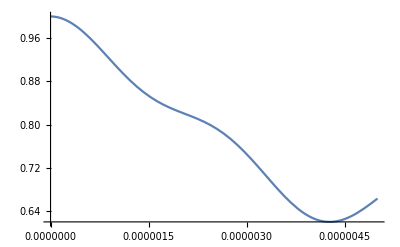

```mathematica
res = SolveSystem[ tStart, tEnd*2, ℋ,2.5897440607094812*^9, density0, IdentityMatrix[9], dephasing];
Plot[res[[3]][[4]] + res[[3]][[5]] + res[[3]][[6]], {t, tStart, tEnd}, PlotLegends->Automatic]
```

### Run simulation

```mathematica
NVbasisStates = IdentityMatrix[9];
RunSimulation[pulseFreqStart,pulseFreqEnd, pulseFreqStep, tStart, tEnd, ℋ,NVbasisStates,density0, dephasing]
totalSimulationTime = simData["totalSimulationTime"];

freqs = Table[ simData["allstates"][[1]][[i]][[1]],{i, 1, Length[simData["allstates"][[1]]]}];
simData["T(1)"]= Table[ {freqs[[i]],  simData["allstates"][[1]][[i]][[2]] + simData["allstates"][[2]][[i]][[2]] + simData["allstates"][[3]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(0)"]= Table[ {freqs[[i]],  simData["allstates"][[4]][[i]][[2]] + simData["allstates"][[5]][[i]][[2]] + simData["allstates"][[6]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(-1)"]= Table[ {freqs[[i]],  simData["allstates"][[7]][[i]][[2]] + simData["allstates"][[8]][[i]][[2]] + simData["allstates"][[9]][[i]][[2]]},  {i, 1, Length[freqs]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.41719×10^-7}. NIntegrate obtained 3.06747×10^-12+0. ⅈ and 1.54116×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {9.08125×10^-7}. NIntegrate obtained 5.21284×10^-12-3.04766×10^-28 ⅈ and 1.09577×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.78438×10^-7}. NIntegrate obtained 5.29002×10^-12+0. ⅈ and 8.07704×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Total time taken (min) = 80.8101

### Results

#### Full simulation results

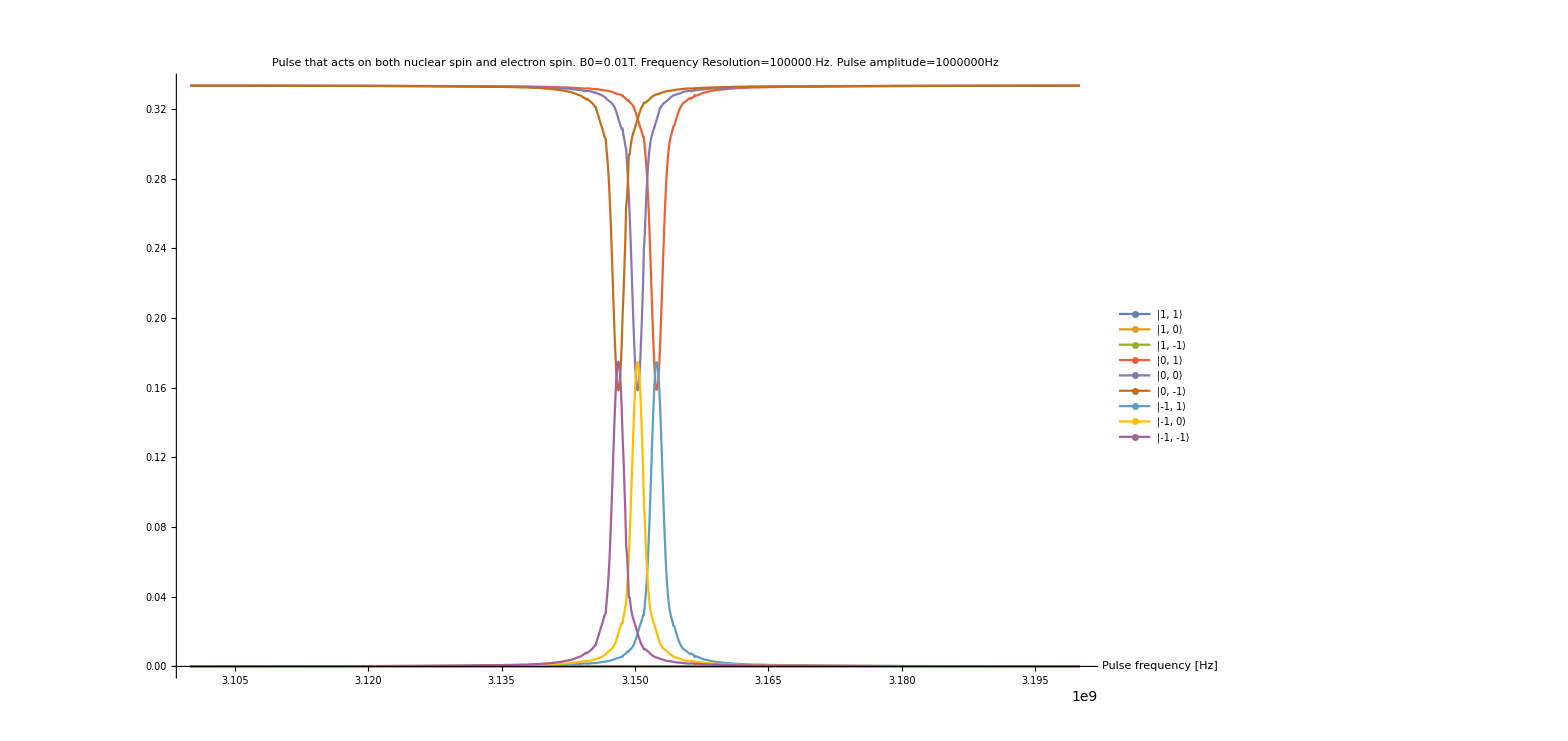

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
fullplot = ListPlot[simData["allstates"], PlotLegends ->LineLegend[fullPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full},Joined-> True,PlotMarkers->None, ImageSize -> 1200 ]
```

#### ESR Plot

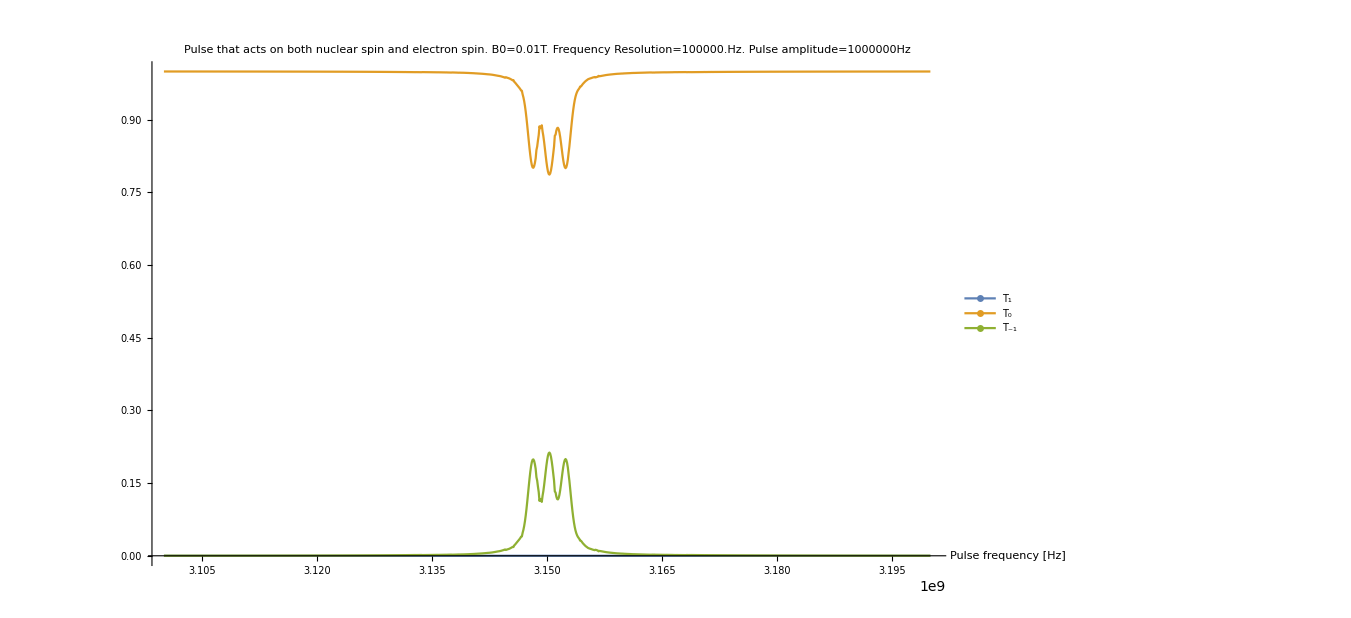

```mathematica
esrPlotlegend = {"T_1", "T_0", "T_-1"};
esrplot = ListPlot[{simData["T(1)"], simData["T(0)"], simData["T(-1)"]}, PlotLegends ->LineLegend[esrPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full}, ImageSize -> 1000 , Joined->True]
```

### Save simulation data

```mathematica
CreateDirectory["./" <> resultsFolder <> fileNamePrefix];
fpre =  "./" <> resultsFolder <> fileNamePrefix <> "/" <> fileNamePrefix;

Export[fpre<> "_data_T(1).csv",simData["T(1)"] ];
Export[fpre<> "_data_T(0).csv",simData["T(0)"]  ];
Export[fpre<> "_data_T(-1).csv",simData["T(-1)"]  ];

(* Save the ESR data *)
Do[
stateStr = "state(" <>ToString[1- ( (i- 1)/3 // Floor)] <> "," <> ToString[1- Mod[i-1, 3]] <>")";
Export[fpre<>"_data_"<> stateStr <> ".csv",simData[i] ];
,{i, 1, 9}]

Export[fpre<> "_spectrum.csv", hamiltonianSpectrum];
Export[fpre<> "_ESRplot.pdf", esrplot];
Export[fpre<> "_fullplot.pdf", fullplot];
Save[ fpre <> "_params.wl", {  comments, totalSimulationTime, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,dephasing,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs}];
```

## No spin-bath 3

### Initialisation

#### NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

#### Simulation parameters

```mathematica
pulseAmplitude = 1*10^6; (* [Hz] *)
pulseAmplitudeE = pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2*^9; (* [Hz] *)
pulseFreqEnd =3.5*^9; (* [Hz] *) 
pulseFreqStep = 5*10^6; (* [Hz] *) 
calculations =Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 5*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 301

#### Setup Hamiltonian

```mathematica
spins = {1, 1};
hilbertSubspaceDimensions = 2*spins + 1;
totalHilbertSpaceDimension = Apply[Times, hilbertSubspaceDimensions];

ℋHF =  SpinSpinHamiltonian[
spins,
{
{1 -> 2, Ahf}
}
];

ℋzfs =  SpinSpinHamiltonian[
spins,
{{1 -> 1, {0, 0,Dzfs}},
{2 -> 2, {0, 0, Pzfs}}}
] ;

ℋzee = ZeemanHamiltonian[spins, {ωs, ωI, 0}];

ℋNV = ℋHF + ℋzfs + ℋzee;

ℋCop =  (pulseAmplitudeE* FullHilbertSpaceOperator[ { 1-> SpinMatrixX[1] }, hilbertSubspaceDimensions ]  + pulseAmplitudeN * FullHilbertSpaceOperator[ { 2-> SpinMatrixX[1] }, hilbertSubspaceDimensions ] );

ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];

dephasing = ConstantArray[0, {totalHilbertSpaceDimension, totalHilbertSpaceDimension}];
Do[ dephasing[[i,i]] = 0, {i, 1, Length[dephasing]}]; (* Set the off-diagonal coefficients to 0 *)
```

#### Energy spectrum of the unperturbed Hamiltonian

In terms of the eigenstates of the Hamiltonian

```mathematica
hamiltonianSpectrum = NVCenterEnergySpectrum[ℋNV]; 
hamiltonianSpectrum[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | {-0.00066556 |0,-1⟩,1. |-1,0⟩} | -1.
3.1475×10^9 | {2.49943×10^-6 |1,-1⟩,-0.000667198 |0,0⟩,1. |-1,1⟩} | 0.
3.14312×10^9 | {1. |-1,-1⟩} | -2.
2.58975×10^9 | {1. |1,0⟩,-0.000809353 |0,1⟩} | 1.
2.58692×10^9 | {1. |1,-1⟩,-0.000811772 |0,0⟩,-3.04104×10^-6 |-1,1⟩} | 0.
2.58266×10^9 | {1. |1,1⟩} | 2.
-3105.84 | {0.000811774 |1,-1⟩,0.999999 |0,0⟩,0.000667196 |-1,1⟩} | 0.
-4.92093×10^6 | {0.000809353 |1,0⟩,1. |0,1⟩} | 1.
-4.98216×10^6 | {1. |0,-1⟩,0.00066556 |-1,0⟩} | -1.)

In terms of eigenstates of the spin triplet and nuclear spin

```mathematica
hamiltonianSpectrumPure = NVCenterEnergySpectrum2[ℋ[0,0]];
hamiltonianSpectrumPure[[2]]
```

(E | |ψ_E⟩ | ⟨J_z⟩
--- | --- | ---
3.15026×10^9 | |-1,0⟩ | -1
3.1475×10^9 | |-1,1⟩ | 0
3.14312×10^9 | |-1,-1⟩ | -2
2.58974×10^9 | |1,0⟩ | 1
2.58692×10^9 | |1,-1⟩ | 0
2.58266×10^9 | |1,1⟩ | 2
0. | |0,0⟩ | 0
-4.91923×10^6 | |0,1⟩ | 1
-4.98077×10^6 | |0,-1⟩ | -1)

#### Initial state

```mathematica
density0 = 1/3(Outer[Times,  IdentityMatrix[9][[4]],  IdentityMatrix[9][[4]]] + Outer[Times,  IdentityMatrix[9][[5]],  IdentityMatrix[9][[5]]] +Outer[Times,  IdentityMatrix[9][[6]],  IdentityMatrix[9][[6]]]);
```

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_NO_SPIN_BATH"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Pulse that acts on both nuclear spin and electron spin",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Rabi Oscillations

```mathematica
res = SolveSystem[ tStart, tEnd*2, ℋ,2.5897440607094812*^9, density0, IdentityMatrix[9], dephasing];
Plot[res[[3]][[4]] + res[[3]][[5]] + res[[3]][[6]], {t, tStart, tEnd}, PlotLegends->Automatic]
```

-Graphics-

### Run simulation

```mathematica
NVbasisStates = IdentityMatrix[9];
RunSimulation[pulseFreqStart,pulseFreqEnd, pulseFreqStep, tStart, tEnd, ℋ,NVbasisStates,density0, dephasing]
totalSimulationTime = simData["totalSimulationTime"];

freqs = Table[ simData["allstates"][[1]][[i]][[1]],{i, 1, Length[simData["allstates"][[1]]]}];
simData["T(1)"]= Table[ {freqs[[i]],  simData["allstates"][[1]][[i]][[2]] + simData["allstates"][[2]][[i]][[2]] + simData["allstates"][[3]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(0)"]= Table[ {freqs[[i]],  simData["allstates"][[4]][[i]][[2]] + simData["allstates"][[5]][[i]][[2]] + simData["allstates"][[6]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(-1)"]= Table[ {freqs[[i]],  simData["allstates"][[7]][[i]][[2]] + simData["allstates"][[8]][[i]][[2]] + simData["allstates"][[9]][[i]][[2]]},  {i, 1, Length[freqs]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.9474884712877843069906912099823609318960393466113600879907608032×10^-6}. NIntegrate obtained 9.28388×10^-13+0. ⅈ and 1.20561×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {2.75383×10^-6}. NIntegrate obtained 2.99495×10^-12+3.65182×10^-28 ⅈ and 2.8582×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {3.86711×10^-6}. NIntegrate obtained 3.14156×10^-12+0. ⅈ and 1.35372×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Total time taken (min) = 24.4965

### Results

#### Full simulation results

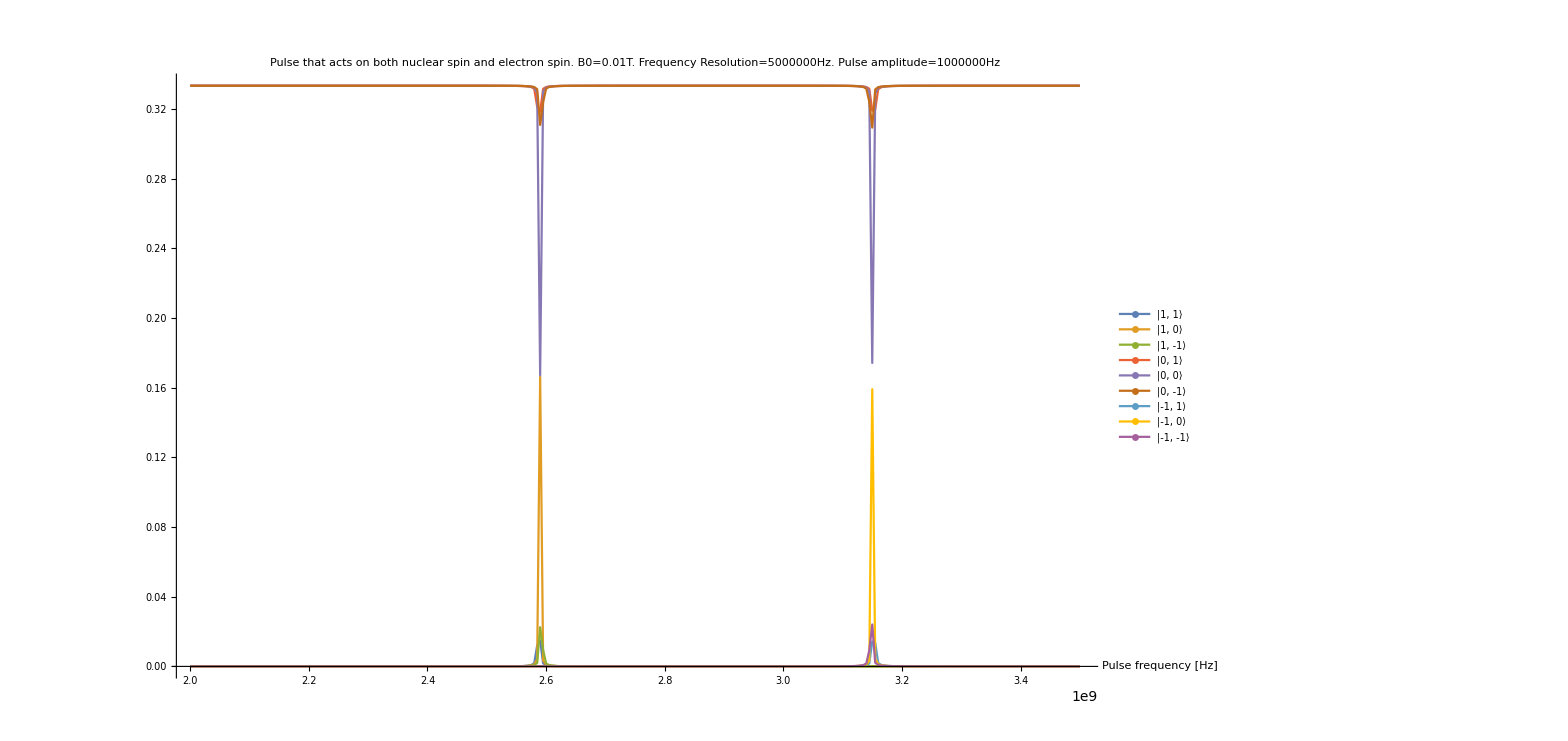

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
fullplot = ListPlot[simData["allstates"], PlotLegends ->LineLegend[fullPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full},Joined-> True,PlotMarkers->None, ImageSize -> 1200 ]
```

#### ESR Plot

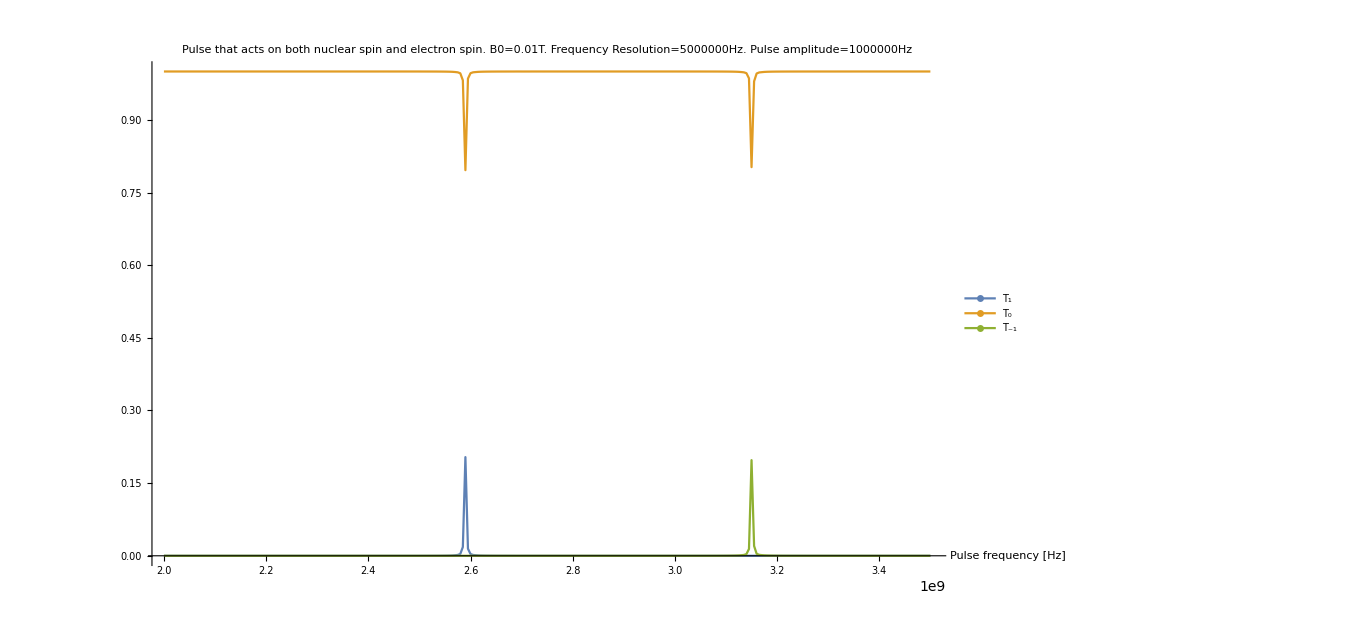

```mathematica
esrPlotlegend = {"T_1", "T_0", "T_-1"};
esrplot = ListPlot[{simData["T(1)"], simData["T(0)"], simData["T(-1)"]}, PlotLegends ->LineLegend[esrPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full}, ImageSize -> 1000 , Joined->True]
```

### Save simulation data

```mathematica
CreateDirectory["./" <> resultsFolder <> fileNamePrefix];
fpre =  "./" <> resultsFolder <> fileNamePrefix <> "/" <> fileNamePrefix;

Export[fpre<> "_data_T(1).csv",simData["T(1)"] ];
Export[fpre<> "_data_T(0).csv",simData["T(0)"]  ];
Export[fpre<> "_data_T(-1).csv",simData["T(-1)"]  ];

(* Save the ESR data *)
Do[
stateStr = "state(" <>ToString[1- ( (i- 1)/3 // Floor)] <> "," <> ToString[1- Mod[i-1, 3]] <>")";
Export[fpre<>"_data_"<> stateStr <> ".csv",simData[i] ];
,{i, 1, 9}]

Export[fpre<> "_spectrum.csv", hamiltonianSpectrum];
Export[fpre<> "_ESRplot.pdf", esrplot];
Export[fpre<> "_fullplot.pdf", fullplot];
Save[ fpre <> "_params.wl", {  comments, totalSimulationTime, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,dephasing,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs}];
```

## Truncated Hamiltonian (m_s= 0, +1) (No spin-bath)

### Initialisation

#### NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

#### Simulation parameters

```mathematica
pulseAmplitude = 7*10^6; (* [Hz] *)
pulseAmplitudeE = pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.58*^9; (* [Hz] *)
pulseFreqEnd =2.6*^9; (* [Hz] *) 
pulseFreqStep = 0.01*10^6; (* [Hz] *) 
calculations =Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 5*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 2001

#### Setup Hamiltonian

```mathematica
totalHilbertSpaceDimension = 2*3;

electronSx = KroneckerProduct[SpinMatrixX[1][[ 1;;2, 1;;2 ]], IdentityMatrix[3]];
electronSy = KroneckerProduct[SpinMatrixY[1][[ 1;;2, 1;;2 ]], IdentityMatrix[3]];
electronSz = KroneckerProduct[SpinMatrixZ[1][[ 1;;2, 1;;2 ]], IdentityMatrix[3]];
nucleusIx = KroneckerProduct[IdentityMatrix[2], SpinMatrixX[1]];
nucleusIy = KroneckerProduct[IdentityMatrix[2], SpinMatrixY[1]];
nucleusIz = KroneckerProduct[IdentityMatrix[2], SpinMatrixZ[1]];

ℋHF = Ahf[[1]]* electronSx.nucleusIx + Ahf[[2]] *electronSy.nucleusIy +  Ahf[[3]] *electronSz.nucleusIz;

ℋzfs = Dzfs * electronSz.electronSz + Pzfs* nucleusIz.nucleusIz;

ℋzee = ωs * electronSz + ωI* nucleusIz;

ℋNV = ℋHF + ℋzfs + ℋzee;

ℋCop = pulseAmplitudeE*electronSx + pulseAmplitudeN*nucleusIx;
ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];
```

Construct the basis state vectors for the NV-center. This unwieldy way of doing it is didactic rather than efficient, the end result is simply an IdentityMatrix[6].

```mathematica
basisStates = {
{1, 0} ⊗ {1, 0, 0} // Flatten,
{1, 0} ⊗ {0, 1, 0} // Flatten,
{1, 0} ⊗ {0, 0, 1} // Flatten,
{0, 1} ⊗ {1, 0, 0} // Flatten,
{0, 1} ⊗ {0, 1, 0} // Flatten,
{0, 1} ⊗ {0, 0, 1} // Flatten
};

dephasing = ConstantArray[0, {totalHilbertSpaceDimension, totalHilbertSpaceDimension}];
Do[ dephasing[[i,i]] = 0, {i, 1, Length[dephasing]}]; (* Set the off-diagonal coefficients to 0 *)
```

#### Initial state

```mathematica
density0 = 1/3(Outer[Times, basisStates[[4]], basisStates[[4]]] + Outer[Times, basisStates[[5]], basisStates[[5]]] + Outer[Times, basisStates[[6]], basisStates[[6]]]);
```

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_TRUNCATED"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Truncated electron spin matrix, containing only ms=0 and ms=+1.",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Rabi Oscillations

```mathematica
res = SolveSystem[ tStart, tEnd, ℋ,2.5897440607094812*^9, density0, basisStates, dephasing];
Plot[res[[3]][[4]] + res[[3]][[5]] + res[[3]][[6]], {t, tStart, tEnd}, PlotLegends->Automatic]
```

### Run simulation

```mathematica
RunSimulation[pulseFreqStart,pulseFreqEnd, pulseFreqStep, tStart, tEnd, ℋ,basisStates,density0, dephasing];
totalSimulationTime = simData["totalSimulationTime"];
```

```mathematica
freqs = Table[ simData["allstates"][[1]][[i]][[1]],{i, 1, Length[simData["allstates"][[1]]]}];
simData["T(1)"]= Table[ {freqs[[i]],  simData["allstates"][[1]][[i]][[2]] + simData["allstates"][[2]][[i]][[2]] + simData["allstates"][[3]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(0)"]= Table[ {freqs[[i]],  simData["allstates"][[4]][[i]][[2]] + simData["allstates"][[5]][[i]][[2]] + simData["allstates"][[6]][[i]][[2]]},  {i, 1, Length[freqs]}];
```

#### Full simulation results

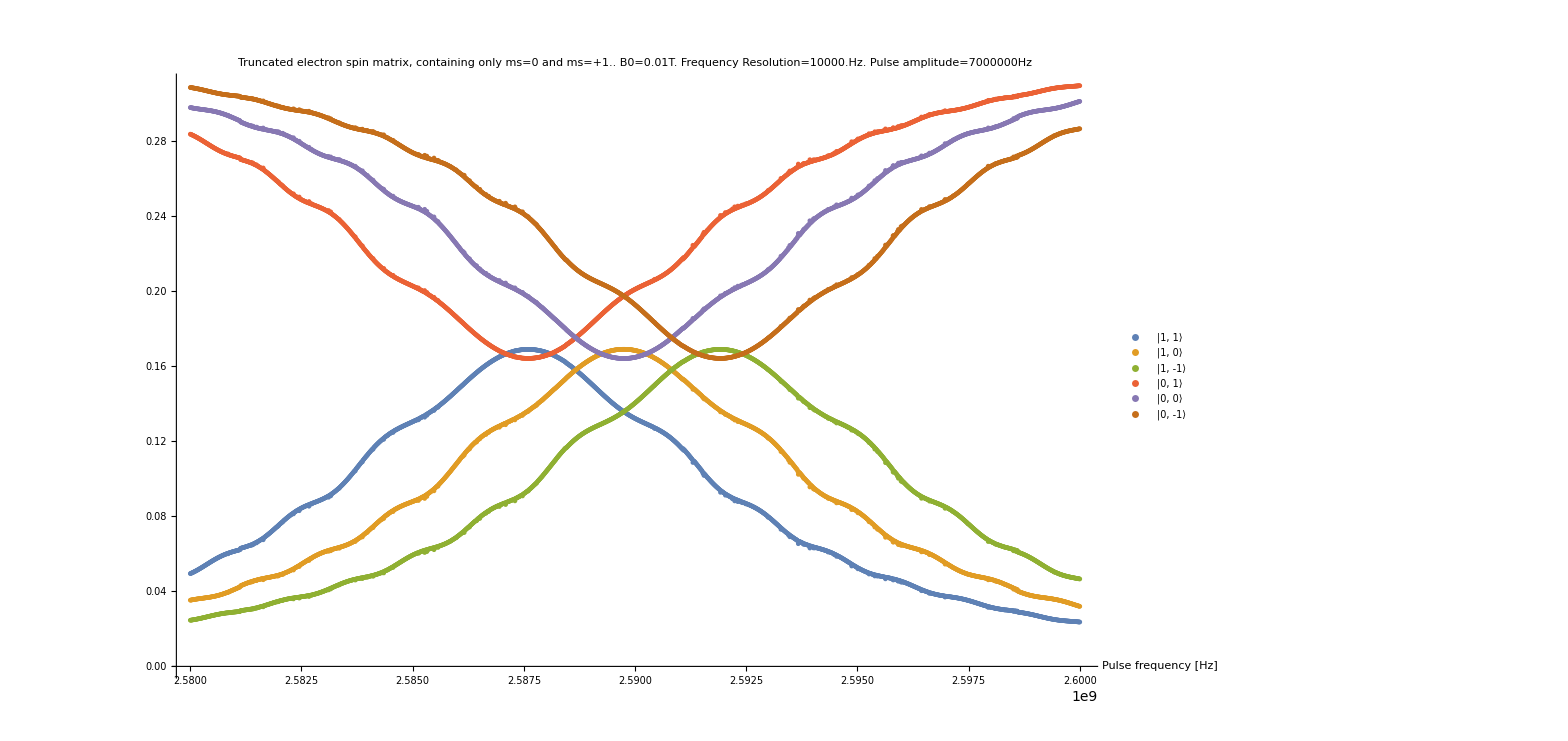

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
fullplot = ListPlot[simData["allstates"], PlotLegends ->LineLegend[fullPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full},Joined-> False,PlotMarkers-> None, ImageSize -> 1200 ]
```

#### ESR Plot

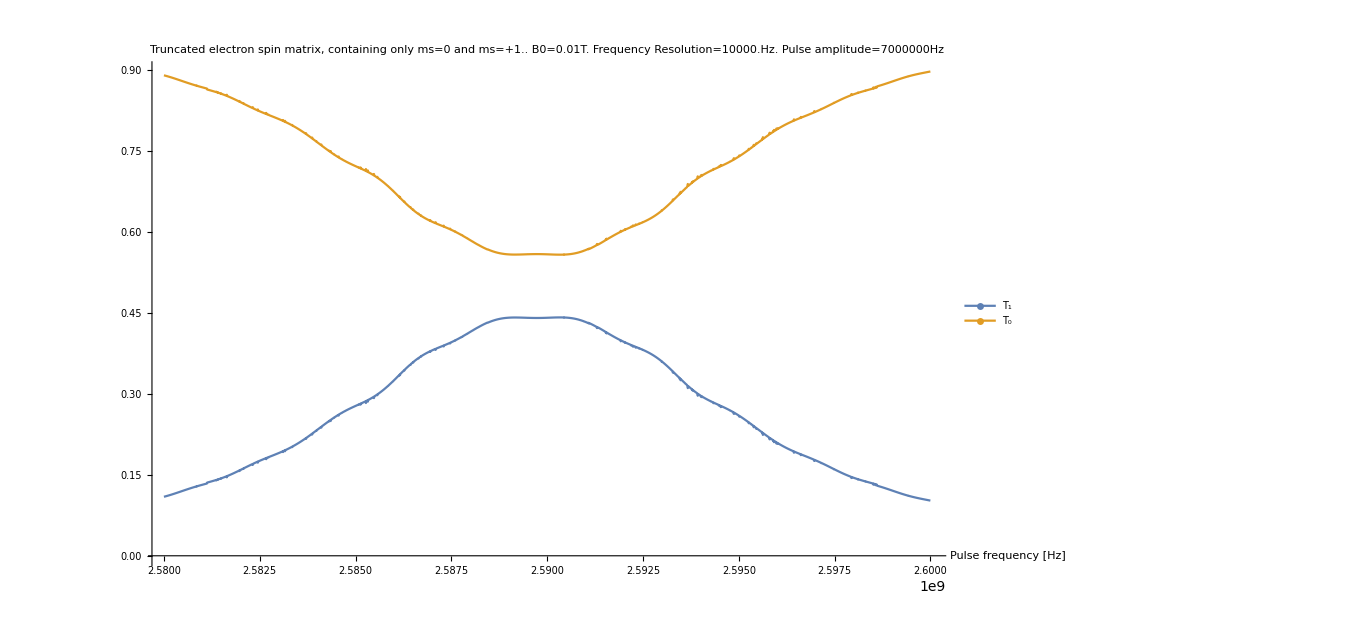

```mathematica
esrPlotlegend = {"T_1", "T_0"};
esrplot = ListPlot[{simData["T(1)"], simData["T(0)"]}, PlotLegends ->LineLegend[esrPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full}, ImageSize -> 1000 , Joined->True]
```

### Save simulation data

```mathematica
CreateDirectory["./" <> resultsFolder <> fileNamePrefix];
fpre =  "./" <> resultsFolder <> fileNamePrefix <> "/" <> fileNamePrefix;

Export[fpre<> "_data_T(1).csv",simData["T(1)"] ];
Export[fpre<> "_data_T(0).csv",simData["T(0)"]  ];
Export[fpre<> "_data_T(-1).csv",simData["T(-1)"]  ];

(* Save the ESR data *)
Do[
stateStr = "state(" <>ToString[1- ( (i- 1)/3 // Floor)] <> "," <> ToString[1- Mod[i-1, 3]] <>")";
Export[fpre<>"_data_"<> stateStr <> ".csv",simData[i] ];
,{i, 1, 9}]

Export[fpre<> "_ESRplot.pdf", esrplot];
Export[fpre<> "_fullplot.pdf", fullplot];
Save[ fpre <> "_params.wl", {  comments, totalSimulationTime, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs}];
```

## Truncated Hamiltonian (m_s= 0, +1) (one extra spin)

The system we are considering is the NV-center (with a truncated Hamiltonian), interact with a spin-1/2 particle.

### Initialisation

#### NV-Centre constants

```mathematica
γN = 19.331*10^6; (* Gyromagnetic ratio for^14 N [s^-1 T^-1] *)
γe = 1.7609*10^11; (* Gyromagnetic ratio for e- [rad s^-1 T^-1] *)
Ahf = { -2.1*10^6, -2.1*10^6, -2.16*10^6 }; (* Hyperfine interaction (x,y,z) [Hz] *)
Dzfs = 2870*10^6 ; (* Zero-field-splitting for electron triplet [Hz] *)
Pzfs = -4.95*10^6 ; (* Zero-field-splitting for^14 N [Hz] *)
```

Interaction parameters for the NV-center interaction with the spin-1/2 particle

```mathematica
ke = {10^6, 10^6,10^6};
kI = {-10^5, -10^5,-10^5};
```

#### Simulation parameters

```mathematica
pulseAmplitude = 7*10^6; (* [Hz] *)
pulseAmplitudeE = pulseAmplitude; (* [Hz] *)
pulseAmplitudeN = pulseAmplitude * γN/γe; (* [Hz] *)
pulsePhase = 0;

pulseFreqStart = 2.58*^9; (* [Hz] *)
pulseFreqEnd =2.6*^9; (* [Hz] *) 
pulseFreqStep = 1*10^6; (* [Hz] *) 
calculations =Table[f, {f, pulseFreqStart, pulseFreqEnd, pulseFreqStep}] // Length;

tStart = 0; (* Start-time of NDSolve [s] *)
tEnd = 2.5*10^-6; (* End-time of NDSolve [s] *)

B0 =100 *10^-4 (* DC Applied field [T] *);
ωs= (-γe B0)/(2π); (* [Hz] *)
ωI=(γN B0)/(2π); (* [Hz] *)

Print["Number of calculations: ", calculations];
```

Number of calculations: 21

#### Setup Hamiltonian

```mathematica
totalHilbertSpaceDimension = 2*3*2;

electronSx = KroneckerProduct[KroneckerProduct[SpinMatrixX[1][[ 1;;2, 1;;2 ]], IdentityMatrix[3]], IdentityMatrix[2]];
electronSy = KroneckerProduct[KroneckerProduct[SpinMatrixY[1][[ 1;;2, 1;;2 ]], IdentityMatrix[3]], IdentityMatrix[2]];
electronSz = KroneckerProduct[KroneckerProduct[SpinMatrixZ[1][[ 1;;2, 1;;2 ]], IdentityMatrix[3]], IdentityMatrix[2]];
nucleusIx = KroneckerProduct[KroneckerProduct[IdentityMatrix[2], SpinMatrixX[1]], IdentityMatrix[2]];
nucleusIy = KroneckerProduct[KroneckerProduct[IdentityMatrix[2], SpinMatrixY[1]], IdentityMatrix[2]];
nucleusIz = KroneckerProduct[KroneckerProduct[IdentityMatrix[2], SpinMatrixZ[1]], IdentityMatrix[2]];
spinbathSx = KroneckerProduct[KroneckerProduct[IdentityMatrix[2], IdentityMatrix[3]], SpinMatrixX[1/2]];
spinbathSy = KroneckerProduct[KroneckerProduct[IdentityMatrix[2], IdentityMatrix[3]], SpinMatrixY[1/2]];
spinbathSz = KroneckerProduct[KroneckerProduct[IdentityMatrix[2], IdentityMatrix[3]], SpinMatrixZ[1/2]];

ℋHF = Ahf[[1]]* electronSx.nucleusIx + Ahf[[2]] *electronSy.nucleusIy +  Ahf[[3]] *electronSz.nucleusIz;

ℋzfs = Dzfs * electronSz.electronSz + Pzfs* nucleusIz.nucleusIz;

ℋzee = ωs * electronSz + ωI* nucleusIz;

ℋspinbath = ke[[1]]*electronSx.spinbathSx + ke[[2]]*electronSy.spinbathSy + ke[[3]]*electronSz.spinbathSz +
kI[[1]]*nucleusIx.spinbathSx + kI[[2]]*nucleusIy.spinbathSy + kI[[3]]*nucleusIz.spinbathSz;

ℋNV = ℋHF + ℋzfs + ℋzee + ℋspinbath;

ℋCop = pulseAmplitudeE*electronSx + pulseAmplitudeN*nucleusIx;
ℋC[f_, t_] :=ℋCop * Sin[f t + pulsePhase];

ℋ[f_,t_] := ℋNV  + ℋC[f,t];
```

Construct the basis state vectors for the NV-center. This unwieldy way of doing it is didactic rather than efficient, the end result is simply an IdentityMatrix[6].

```mathematica
basisStates = {
{1, 0} ⊗ {1, 0, 0}⊗{1, 0}// Flatten,
{1, 0} ⊗ {1, 0, 0}⊗{0, 1}// Flatten,
{1, 0} ⊗ {0, 1, 0}⊗{1, 0} // Flatten,
{1, 0} ⊗ {0, 1, 0}⊗{0, 1} // Flatten,
{1, 0} ⊗ {0, 0, 1}⊗{1, 0} // Flatten,
{1, 0} ⊗ {0, 0, 1}⊗{0, 1} // Flatten,
{0, 1} ⊗ {1, 0, 0}⊗{1, 0} // Flatten,
{0, 1} ⊗ {1, 0, 0}⊗{0, 1} // Flatten,
{0, 1} ⊗ {0, 1, 0} ⊗{1, 0}// Flatten,
{0, 1} ⊗ {0, 1, 0}⊗{0, 1} // Flatten,
{0, 1} ⊗ {0, 0, 1}⊗{1, 0}// Flatten,
{0, 1} ⊗ {0, 0, 1}⊗{0, 1} // Flatten
};

dephasing = ConstantArray[0, {totalHilbertSpaceDimension, totalHilbertSpaceDimension}];
Do[ dephasing[[i,i]] = 0, {i, 1, Length[dephasing]}]; (* Set the off-diagonal coefficients to 0 *)
```

#### Initial state

```mathematica
density0 = 1/3(Outer[Times, basisStates[[4]], basisStates[[4]]] + Outer[Times, basisStates[[5]], basisStates[[5]]] + Outer[Times, basisStates[[6]], basisStates[[6]]]);
```

#### Meta

```mathematica
resultsFolder = "results/";
fileNamePrefix = "nv_center_simulation_TRUNCATED_WITH_EXTRA_SPIN"  <> StringReplace[ DateString["ISODateTime"], {":" -> ".", "T" -> "_"}];
comments = StringRiffle[{
"Truncated electron spin matrix, containing only ms=0 and ms=+1.",
StringForm["B0=``T",B0],
StringForm["Frequency Resolution=``Hz", pulseFreqStep],
StringForm["Pulse amplitude=``Hz", pulseAmplitude]
}, ". "];
```

### Rabi Oscillations

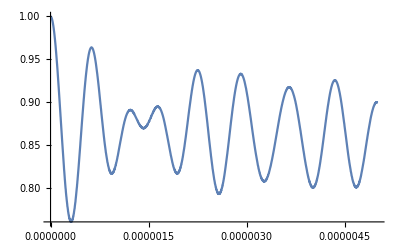

```mathematica
res = SolveSystem[ tStart, tEnd, ℋ,2.5822143875061417*^9, density0, basisStates, dephasing];
Plot[res[[3]][[4]] + res[[3]][[5]] + res[[3]][[6]], {t, tStart, tEnd}, PlotLegends->Automatic]
```

### Run simulation

```mathematica
RunSimulation[pulseFreqStart,pulseFreqEnd, pulseFreqStep, tStart, tEnd, ℋ,basisStates,density0, dephasing];
totalSimulationTime = simData["totalSimulationTime"];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.07418×10^-6}. NIntegrate obtained 1.64077×10^-20-1.67447×10^-38 ⅈ and 2.2722×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.01559×10^-6}. NIntegrate obtained 9.05139×10^-14-2.41159×10^-32 ⅈ and 3.9536×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.95309×10^-6}. NIntegrate obtained 6.09569×10^-14+4.43685×10^-31 ⅈ and 2.46272×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Total time taken (min) = 8.84669

```mathematica
freqs = Table[ simData["allstates"][[1]][[i]][[1]],{i, 1, Length[simData["allstates"][[1]]]}];
simData["T(1)"]= Table[ {freqs[[i]],  simData["allstates"][[1]][[i]][[2]] + simData["allstates"][[2]][[i]][[2]] + simData["allstates"][[3]][[i]][[2]]},  {i, 1, Length[freqs]}];
simData["T(0)"]= Table[ {freqs[[i]],  simData["allstates"][[4]][[i]][[2]] + simData["allstates"][[5]][[i]][[2]] + simData["allstates"][[6]][[i]][[2]]},  {i, 1, Length[freqs]}];
```

#### Full simulation results

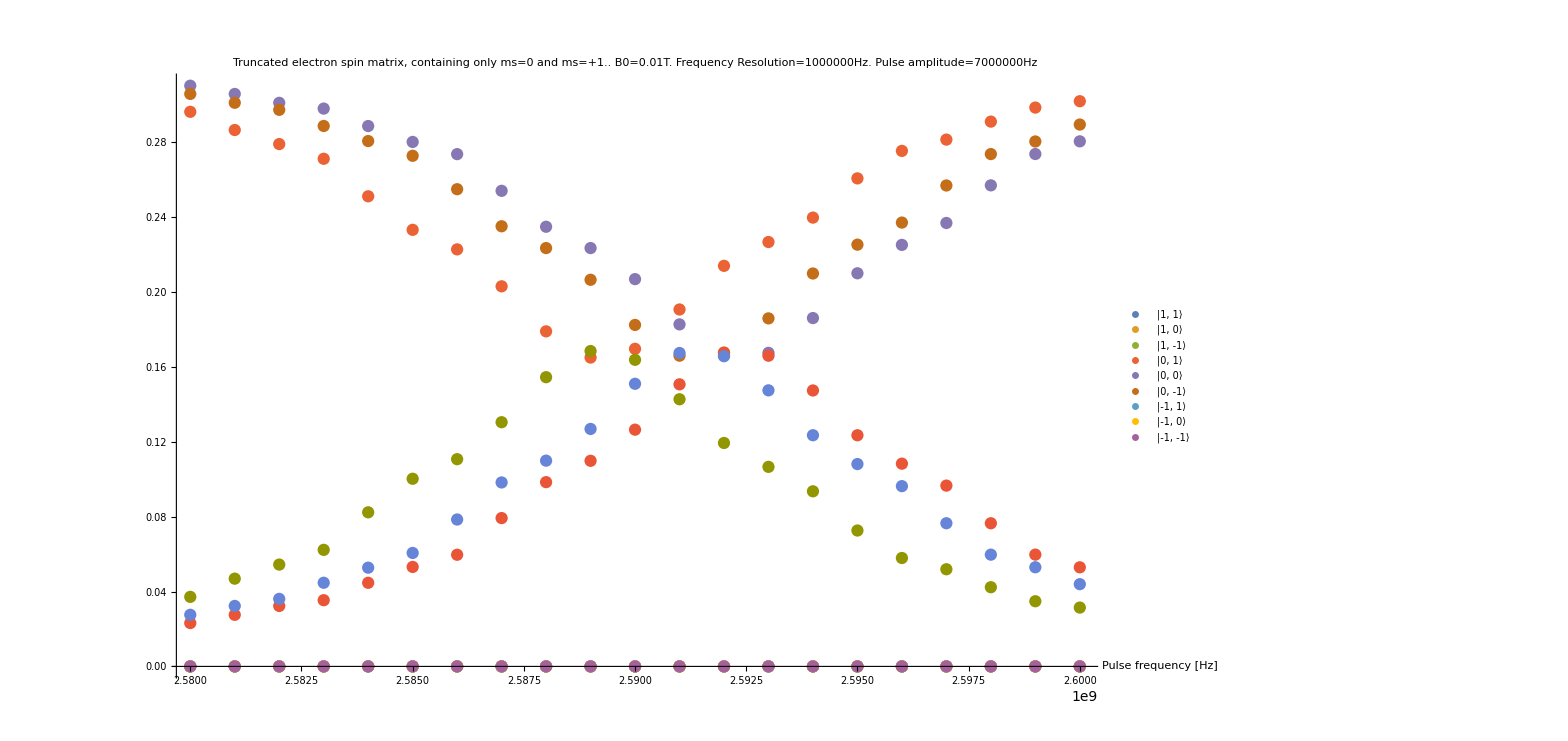

```mathematica
fullPlotlegend = {"|1, 1⟩", "|1, 0⟩", "|1, -1⟩", "|0, 1⟩", "|0, 0⟩", "|0, -1⟩","|-1, 1⟩", "|-1, 0⟩", "|-1, -1⟩"};
fullplot = ListPlot[simData["allstates"], PlotLegends ->LineLegend[fullPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full},Joined-> False,PlotMarkers-> None, ImageSize -> 1200 ]
```

#### ESR Plot

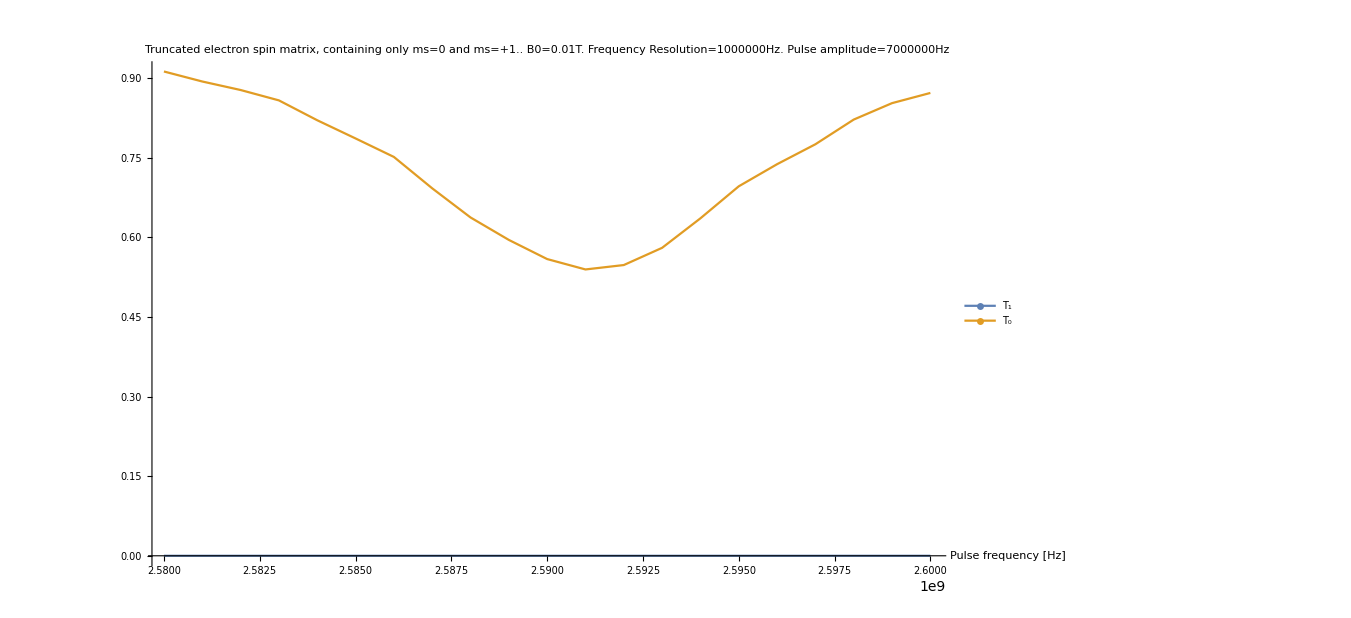

```mathematica
esrPlotlegend = {"T_1", "T_0"};
esrplot = ListPlot[{simData["T(1)"], simData["T(0)"]}, PlotLegends ->LineLegend[esrPlotlegend, LabelStyle-> {Bold, 12}, LegendMarkers -> Graphics[{Thickness[0.2],Line[{{-3,0},{3,0}}]}], LegendMarkerSize->{30,30}],PlotLabel->Style[comments, 12], AxesLabel -> { "Pulse frequency [Hz]"}, PlotRange-> {Full, Full}, ImageSize -> 1000 , Joined->True]
```

### Save simulation data

```mathematica
CreateDirectory["./" <> resultsFolder <> fileNamePrefix];
fpre =  "./" <> resultsFolder <> fileNamePrefix <> "/" <> fileNamePrefix;

Export[fpre<> "_data_T(1).csv",simData["T(1)"] ];
Export[fpre<> "_data_T(0).csv",simData["T(0)"]  ];
Export[fpre<> "_data_T(-1).csv",simData["T(-1)"]  ];

(* Save the ESR data *)
Do[
stateStr = "state(" <>ToString[1- ( (i- 1)/3 // Floor)] <> "," <> ToString[1- Mod[i-1, 3]] <>")";
Export[fpre<>"_data_"<> stateStr <> ".csv",simData[i] ];
,{i, 1, 9}]

Export[fpre<> "_ESRplot.pdf", esrplot];
Export[fpre<> "_fullplot.pdf", fullplot];
Save[ fpre <> "_params.wl", {  comments, totalSimulationTime, pulseAmplitude,pulsePhase,pulseFreqStart,pulseFreqEnd,calculations,pulseFreqStep,γN,γe,B0,ωs,ωI,Ahf,Dzfs,Pzfs}];
```